```mathematica
Qfield[x_]:=(({{0, -1}, {1, 0}}).x)/(2π Max[x.x,0.001])
```

```mathematica
Условия задачи
```

```mathematica
ν=(*1/1000*)10^-5;τ=0.01;eps=0.0001;Vinf={1,0};
```

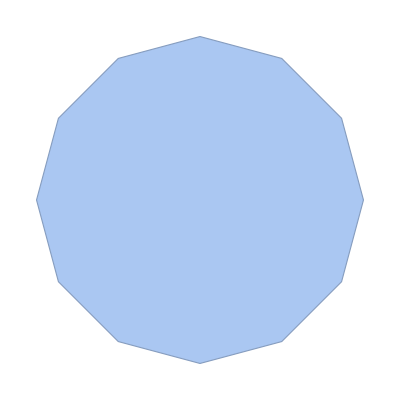

```mathematica
Rdots=Table[{Cos[t],Sin[t]},{t,0,2Pi-0.01,Pi/6}];
Rarea=BoundaryMeshRegion[Rdots,Line[Append[Range[1,Length@Rdots],1]]]
```

```mathematica
Rmids=(RotateLeft@Rdots+Rdots)/2;
Rsides=(RotateLeft@Rdots-Rdots);
rotRsides=RotateLeft@Rsides;
lSides=Table[√(Rsides[[i]].Rsides[[i]]),{i,Length@Rsides}];
```

```mathematica
Rnormals=Transpose@(({{0, -1}, {1, 0}}).Transpose@Rsides);
```

```mathematica
Rnormals=Table[Rnormals[[i]]/(√(Rnormals[[i]].Rnormals[[i]])),{i,Length@Rnormals}];
```

```mathematica
curlDeploy=1.05Rdots;
```

```mathematica
pics={};pics2={};
```

```mathematica
Предварительное составление матрицы и нахождение начальных вихрей
```

```mathematica
L1=Table[Qfield[Rmids[[i]]-curlDeploy[[j]]].Rnormals[[i]],{i,1,Length@Rdots},{j,1,Length@Rdots}];
newGamma=Table[{G[i]},{i,1,Length@Rdots}];
f0=Rnormals.Vinf;
curlsOnPanel={};
curlsInFlow={};
solution=Solve[{L1.newGamma+r==-f0,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]];
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution;
For[i=1,i≤Length@nGammaR-1,i++,AppendTo[curlsOnPanel,{nGammaR[[i]],curlDeploy[[i]]}]];
minCurl=Max[Abs@nGammaR]*0.001;
```

```mathematica
AllCurls=Join[curlsInFlow,curlsOnPanel];
Vfield=Vinf+Sum[First@AllCurls[[i]]Qfield[{x,y}-Last@AllCurls[[i]]],{i,Length@AllCurls}];
```

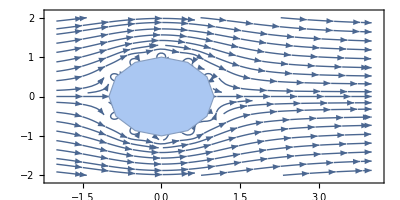

```mathematica
Show[StreamPlot[Vfield,{x,-2,4},{y,-2,2}],Rarea,AspectRatio->1/2]
```

```mathematica
For[k=0,k<100,k++,
AllCurls=Join[curlsInFlow,curlsOnPanel];
f1=ParallelTable[Sum[Rnormals[[i]].Qfield[Rmids[[i]]-Last@AllCurls[[m]]]First@AllCurls[[m]],{m,1,Length@AllCurls}],{i,1,Length@curlDeploy}];
solution=Solve[{L1.newGamma+r==-f0-f1,Sum[newGamma[[i]],{i,Length@newGamma}]==0},Append[First@Transpose@newGamma,r]];
nGammaR=Append[First@Transpose@newGamma,r]/.First@solution;
For[i=1,i≤Length@curlsOnPanel,i++,
If[(Last@curlsOnPanel[[i]]-curlDeploy[[i]]).(Last@curlsOnPanel[[i]]-curlDeploy[[i]])<Min[lSides]^2/8,
curlsOnPanel[[i]][[1]]=curlsOnPanel[[i]][[1]]+nGammaR[[i]];
curlsOnPanel[[i]][[2]]=(Last@curlsOnPanel[[i]]*First@curlsOnPanel[[i]]+curlDeploy[[i]]*nGammaR[[i]])/(First@curlsOnPanel[[i]]+nGammaR[[i]]),
 AppendTo[curlsInFlow,curlsOnPanel[[i]]];(*слабое место, переделать!!!!*)
curlsOnPanel[[i]][[1]]=nGammaR[[i]];
curlsOnPanel[[i]][[2]]=curlDeploy[[i]];
]
(*If[(Last@curlsOnPanel[[i]]-curlDeploy[[i]]).(Last@curlsOnPanel[[i]]-curlDeploy[[i]])<Min[lSides]^2/4,
curlsOnPanel[[i]][[1]]=curlsOnPanel[[i]][[1]]+nGammaR[[i]]
]*)
];
AllCurls=Join[curlsInFlow,curlsOnPanel];

etaR=Table[{x,y}-Rmids[[i]],{i,Length@Rmids}]/eps;(*переделать в соответствии с диссером*)
modEtaR=Table[etaR[[i]].etaR[[i]],{i,Length@Rmids}];
primeR=Table[{x,y}-Last@(AllCurls[[i]]),{i,Length@AllCurls}];
modPrimeR=Table[primeR[[i]].primeR[[i]],{i,Length@AllCurls}];
I2=-Parallelize@Sum[primeR[[i]]/(√modPrimeR[[i]] eps) First@(AllCurls[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@AllCurls}];
I1=Parallelize@Sum[First@(AllCurls[[i]])Exp[-(√modPrimeR[[i]])/eps],{i,Length@AllCurls}];
I3=-Parallelize@Sum[Rnormals[[i]]Exp[-√modEtaR[[i]]],{i,Length@Rnormals}];
(*I3=-Parallelize@Sum[Rnormals[[i]]eps (1-Exp[-(√(Rsides[[i]].Rsides[[i]]))/(2 eps)]),{i,Length@Rnormals}];*)
I0=2π eps^2+Parallelize@Sum[(etaR[[i]].Rnormals[[i]])/modEtaR[[i]](√modEtaR[[i]]+1)Exp[-√modEtaR[[i]]]lSides[[i]],{i,Length@Rnormals}];
Wfield=ν(-I2/I1+I3/I0);
If[Length@curlsInFlow>0,
curlsInFlow=ParallelTable[{First@curlsInFlow[[i]],Last@(curlsInFlow[[i]])+τ (Vfield+Wfield)/.{x->First@Last@(curlsInFlow[[i]])+eps/1000,y->Last@Last@(curlsInFlow[[i]])+eps/1000}},{i,Length@curlsInFlow}];]
curlsOnPanel=ParallelTable[{First@curlsOnPanel[[i]],Last@(curlsOnPanel[[i]])+τ (Vfield+Wfield)/.{x->First@Last@(curlsOnPanel[[i]])+eps/1000,y->Last@Last@(curlsOnPanel[[i]])+eps/1000}},{i,Length@curlsOnPanel}];

(*Ufield[x0_]:=(Vfield+Wfield)/.{x->First@x0,y->Last@x0}*)
(*
curlsOnPanel={};
curlsInFlow={};*)
(*Определяем кандидатов под аннигиляцию и, пока есть такая возможность, без угрызений совести выпиливаем из списка*)
(*curlsToRemove={};*)
For[i=1,i≤Length@curlsOnPanel,i++,If[RegionMember[Rarea,Last@(curlsOnPanel[[i]])] ||Abs@ First@(curlsOnPanel[[i]])<minCurl,curlsOnPanel[[i]][[2]]=curlDeploy[[i]];curlsOnPanel[[i]][[1]]=nGammaR[[i]];];];
(*curlsOnPanel=Delete[curlsOnPanel,curlsToRemove];*)
curlsToRemove={};
For[i=1,i≤Length@curlsInFlow,i++,If[RegionMember[Rarea,Last@(curlsInFlow[[i]])] ||Abs@ First@(curlsInFlow[[i]])<minCurl,AppendTo[curlsToRemove,{i}]];];
curlsInFlow=Delete[curlsInFlow,curlsToRemove];
AllCurls=Join[curlsInFlow,curlsOnPanel];

Vfield=Vinf+Sum[First@AllCurls[[i]]Qfield[{x,y}-Last@AllCurls[[i]]],{i,Length@AllCurls}];
If[Mod[k,5]==0,
AppendTo[pics2,Show[(*ContourPlot[Vfield.Vfield,{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],*)StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]];
CurlsGraph=Table[Graphics[{White,Disk[Last@AllCurls[[i]],1/20]}],{i,Length@AllCurls}];
AppendTo[pics,Show[ContourPlot[0,{x,-2,4},{y,-2,2}],Rarea,CurlsGraph,AspectRatio->1/2]];]]
```

Min::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √(1/4+(-1+(√3)/2)^2)-√((1/2-1/2 Power[«2»])^2+(-1/2+1/2 Power[«2»])^2).

Min::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √(1/4+(1-(√3)/2)^2)-√((1/2-1/2 Power[«2»])^2+(-1/2+1/2 Power[«2»])^2).

Min::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating √2 (-1/2+(√3)/2)-√((1/2-1/2 Power[«2»])^2+(-1/2+1/2 Power[«2»])^2).

General::stop: Further output of Min::meprec will be suppressed during this calculation.

```mathematica
curlsInFlow
curlsOnPanel
```

{{0.578761,{1.32343,-0.423296}},{-1.17252,{1.01789,0.78848}},{-0.403539,{1.23478,0.262274}},{-0.0363015,{1.95214,0.0278921}},{0.163005,{1.2796,0.704851}},{-0.242723,{0.253399,1.13913}},{-0.745331,{0.537486,1.10819}},{0.0154675,{1.13819,-0.566297}},{-0.396806,{-0.544213,0.86775}},{0.038271,{1.2817,0.0918956}},{-1.60859,{-0.0429553,1.24944}},{0.0219075,{-1.87345,-1.06606}},{0.230012,{-1.22801,0.042887}},{-0.0282023,{0.135756,1.41705}},{0.820306,{-0.0458922,-1.03895}},{-0.841725,{1.02339,1.01452}},{-0.22491,{1.4291,-0.468484}},{0.108466,{-0.115712,1.41416}},{0.616933,{-3.79766,1.81576}},{-0.878273,{-0.813366,0.754548}},{0.022916,{-4.62336,3.33087}},{1.06242,{-0.400017,-1.0569}}}

{{0.131347,{1.04911,0.0276145}},{0.30622,{0.880001,0.539699}},{0.089752,{0.62423,1.0798}},{-0.0898972,{-0.00438985,1.04882}},{-0.215853,{-0.256004,0.964745}},{-0.118948,{-0.916273,0.557488}},{-0.241285,{-1.01021,0.0624338}},{0.2748,{-0.845054,-0.541691}},{0.0144953,{-0.525164,-0.916627}},{-0.0140991,{0.,-1.05}},{0.750483,{0.652706,-0.869078}},{0.458371,{0.995415,-0.508493}}}

```mathematica
Length@curlsOnPanel
```

12

```mathematica
Length@pics
```

140

```mathematica
Export["tester2.gif",pics2]
```

tester2.gif

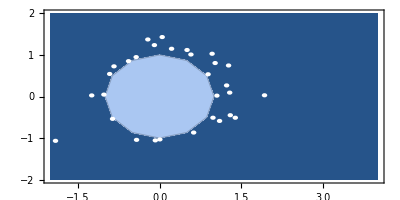

```mathematica
Last@pics
```

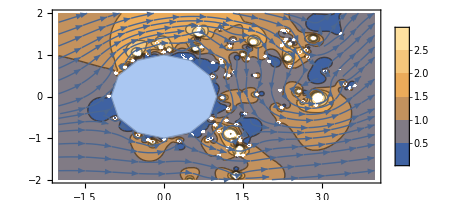

```mathematica
Show[ContourPlot[√(Vfield.Vfield),{x,-2,4},{y,-2,2},PlotLegends->Automatic,PlotRange->{-1,3}],StreamPlot[Vfield,{x,-2,4},{y,-2,2}(*,Mesh->5*)],Rarea,AspectRatio->1/2]
```

```mathematica
minCurl
```

0.00104839